# Some connectivity based cluster validity indices + Amano-Wada indices

## 準備

```mathematica
Needs["HierarchicalClustering`"]
```

```mathematica
Needs["Combinatorica`"]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
(*SetDirectory["/Users/kouamano/gitsrc/ClusteringAdequation/test-data"]*)
```

```mathematica
(*SetDirectory["/Users/amanokou/gitsrc/ClusteringAdequation/test-data"]*)
```

```mathematica
SetDirectory["/home/kamano/gitsrc/ClusteringAdequation/test-data"]
```

/home/kamano/gitsrc/ClusteringAdequation/test-data

```mathematica
(*Get["/home/kamano/gitsrc/MATH_SCRIPT/SCRIPTS/ConnectiveClass.txt"]*)
```

## 基本Programまとめ

minindexをつくる。
Input: dShortMat, Clusteringの結果(クラスタIDのリストのリスト).
output: メンバーID.

最終的に、z[k] = x[k,minindex]; z: medoid of cluster k, x: minindex-th member of cluster k、を求める。

距離行列から特定のクラスタに関する部分距離行列を抜き出す。

```mathematica
subDMat[dmat_,members_]:=Transpose[Transpose[dmat[[members]]][[members]]]
```

部分距離行列をもとに特定のクラスタのargminを求める(minindex)。

```mathematica
argMinDMat[dmat_]:=Module[{sumList},
sumList=Map[Tr[#]&,dmat];
Position[sumList,Min[sumList]][[1]]
]
```

距離行列とクラスタリング結果から各クラスタのmedoidをもとめる。

```mathematica
findMedoidsParCL[dmat_,clusterResult_]:=Map[argMinDMat[subDMat[dmat,#]]&,clusterResult]
```

各クラスタのmedoid番号からもとのサンプル番号を求める。

```mathematica
(*orgIndexFromMedoidParCL[medoids_,clusterResult_]:=Inner[Part,clusterResult,medoids,List]*)
```

```mathematica
orgIndexFromMedoidParCL[clusterResult_,medoids_]:=Module[
{l,fmedoids},
l=Length[medoids];
fmedoids=Flatten[medoids];
Table[clusterResult[[i]][[medoids[[i]]]],{i,l}]
]
```

行列から対角要素をdropする(サイズは縮小)。

```mathematica
dropDiagonal[mat_]:=Table[Drop[mat[[n]],{n}],{n,Length[mat]}]
```

## Sample

```mathematica
sample={{1,1,2},
{2,1,4},
{3,3,5},
{4,5,4},
{3,2,5},
{1,3,1}
}
```

{{1,1,2},{2,1,4},{3,3,5},{4,5,4},{3,2,5},{1,3,1}}

## FindClusters Examples

```mathematica
fc=FindClusters[sample->Range[Length[sample]],3,Method->"Agglomerate"]
```

{{1,6},{2,3,5},{4}}

## DistanceMatrix

```mathematica
sampleDmat=Outer[EuclideanDistance,sample//N,sample,1]
```

{{0.,2.23607,4.12311,5.38516,3.74166,2.23607},{2.23607,0.,2.44949,4.47214,1.73205,3.74166},{4.12311,2.44949,0.,2.44949,1.,4.47214},{5.38516,4.47214,2.44949,0.,3.31662,4.69042},{3.74166,1.73205,1.,3.31662,0.,4.58258},{2.23607,3.74166,4.47214,4.69042,4.58258,0.}}

```mathematica
(*Export["sample.dmat",sampleDmat,"TSV"]*)
```

RNG_d  df=sample.dmat  size=6 > sample.RNGd

mk_d _short _mat  loop=6  dsize=6  ef=sample.RNGd > sample.dsmat

```mathematica
sampleDSmat=Import["sample.dsmat","Table"]
```

{{2.23607,2.23607,2.23607,2.44949,2.23607,2.23607},{2.23607,1.73205,1.73205,2.44949,1.73205,2.23607},{2.23607,1.73205,1.,2.44949,1.,2.23607},{2.44949,2.44949,2.44949,2.44949,2.44949,2.44949},{2.23607,1.73205,1.,2.44949,1.,2.23607},{2.23607,2.23607,2.23607,2.44949,2.23607,2.23607}}

```mathematica
sampleDSmatZeroself=ReplacePart[sampleDSmat,{x_,x_}->0]
```

{{0,2.23607,2.23607,2.44949,2.23607,2.23607},{2.23607,0,1.73205,2.44949,1.73205,2.23607},{2.23607,1.73205,0,2.44949,1.,2.23607},{2.44949,2.44949,2.44949,0,2.44949,2.44949},{2.23607,1.73205,1.,2.44949,0,2.23607},{2.23607,2.23607,2.23607,2.44949,2.23607,0}}

## cDB

cDB = Sum(R[i],{i,1,K}) / K   ; K:クラスタ数
R[i] = Max[{j,j≠i}]((S[i]+S[j])/d[i,j])   ; i:クラスタi, d[i,j]: ユークリッド距離行列
S[i] = Sum(dshort(x,z[i]),{x,x∈C[i]}) / n[i]   ; z[i]:medoid of cluster i, n[i]:number of cluster points.

### Program

距離行列とクラスタリング結果から各クラスタのmedoidをもとめる。

```mathematica
??findMedoidsParCL
```

Global`findMedoidsParCL

findMedoidsParCL[dmat_,clusterResult_]:=(argMinDMat[subDMat[dmat,#1]]&)/@clusterResult

各クラスタのmedoid番号からもとのサンプル番号を求める。

```mathematica
??orgIndexFromMedoidParCL
```

Global`orgIndexFromMedoidParCL

orgIndexFromMedoidParCL[clusterResult_,medoids_]:=Module[{l,fmedoids},l=Length[medoids];fmedoids=Flatten[medoids];Table[clusterResult⟦i⟧⟦medoids⟦i⟧⟧,{i,l}]]

```mathematica
connectiveClass`s[dshortMatZeroself_,clMembers_,medoidIndex_]:=Tr[dshortMatZeroself[[medoidIndex,clMembers]]]/Length[clMembers]
```

```mathematica
connectiveClass`r[edMat_,dshortMatZeroself_,cls_,medoids_,i_]:=Module[{js},
js=Drop[Range[Length[cls]],{i}];
Max[  Map[(connectiveClass`s[dshortMatZeroself,cls[[i]],medoids[[i]]]+connectiveClass`s[dshortMatZeroself,cls[[#]],medoids[[#]]])/edMat[[i,#]]&,js]  
]
]
```

```mathematica
cDB[edMat_,dshortMatZeroself_,cls_,medoids_]:=Tr[Table[connectiveClass`r[edMat,dshortMatZeroself,cls,medoids,i],{i,Length[cls]}]]
```

```mathematica
cDB[edMat_,dshortMatZeroself_,cls_]:=Module[{sampleMedoids},
sampleMedoids=(orgIndexFromMedoidParCL[fc,findMedoidsParCL[edMat,cls]]//Flatten);
Tr[Table[connectiveClass`r[edMat,dshortMatZeroself,cls,sampleMedoids,i],{i,Length[cls]}]]
]
```

### Examples

```mathematica
cDB[sampleDmat,sampleDSmatZeroself,fc]
```

2.18633

```mathematica
sampleDSmat[[1,{1,4,6}]]
```

{2.23607,2.44949,2.23607}

## cDunn

cDunn = Min[i, 1, K] (Min[j,1,K ; j≠i]( d(C[i],C[j])/Max[k,1,K](delta(C[k])) ))
delta(C) = Max[x,y ∈ C](dshort(x,y)) ; diameter
d(C[i],C[j]) = Min[x∈C[i] , y∈C[j]](dshort(x,y))
C : クラスタ、K : クラスタ数

### Program

```mathematica
connectiveClass`d[cl1_,cl2_,dshortMatZeroself_]:=Module[
{outer},
outer=Flatten[Outer[List,cl1,cl2,1],1];
Min[Map[dshortMatZeroself[[#[[1]],#[[2]]]]&,outer]]
]
```

```mathematica
connectiveClass`delta[cl_,dshortMatZeroself_]:=Module[
{subset},
subset=Subsets[cl,{2}];
If[Length[subset]==0,0,Max[Map[dshortMatZeroself[[#[[1]],#[[2]]]]&,subset]]]
]
```

```mathematica
cDunn[cls_,dshortMatZeroself_]:=Module[
{numCls,maxdelta,subset},
numCls=Length[cls];
maxdelta=Max[Map[connectiveClass`delta[#,dshortMatZeroself]&,cls]];
subset=Subsets[cls,{2}];
Min[Map[connectiveClass`d[#[[1]],#[[2]],dshortMatZeroself]&,subset]]/maxdelta
]
```

### Examples

```mathematica
cDunn[fc,sampleDSmatZeroself]
```

1.

```mathematica
delta[fc[[3]],sampleDSmatZeroself]
```

delta[{4},{{0,2.23607,2.23607,2.44949,2.23607,2.23607},{2.23607,0,1.73205,2.44949,1.73205,2.23607},{2.23607,1.73205,0,2.44949,1.,2.23607},{2.44949,2.44949,2.44949,0,2.44949,2.44949},{2.23607,1.73205,1.,2.44949,0,2.23607},{2.23607,2.23607,2.23607,2.44949,2.23607,0}}]

```mathematica
Begin["connectiveClass`"]
```

connectiveClass`

```mathematica
d[fc[[2]],fc[[3]],sampleDSmatZeroself]
```

2.44949

```mathematica
End[]
```

connectiveClass`

```mathematica
d[fc[[2]],fc[[3]],sampleDSmatZeroself]
```

d[{2,3,5},{4},{{0,2.23607,2.23607,2.44949,2.23607,2.23607},{2.23607,0,1.73205,2.44949,1.73205,2.23607},{2.23607,1.73205,0,2.44949,1.,2.23607},{2.44949,2.44949,2.44949,0,2.44949,2.44949},{2.23607,1.73205,1.,2.44949,0,2.23607},{2.23607,2.23607,2.23607,2.44949,2.23607,0}}]

```mathematica
cDunn[fc,sampleDSmatZeroself]
```

1.

## cGDunn

cGDunn = Min[1,s,K](Min[1,t,K ; t!=s]( (Gd(C[s],C[t]))/(Max[1,k,K](Gdelta(C[k]))) )) .
Gdelta(S) = 2 (Sum[x∈S](dshort(x,z[S]))) / Length(S) ; z[S] ; medoid of S ; S : クラスタ .
Gd(S,T) = (1/(Length(S) Length(T))) Sum[x∈S,y∈T](dshort(x,y)) ; S,T : クラスタ .

### Program

```mathematica
connectiveClass`Gdelta[cls_,medoid_,dshortMatZeroself_]:=
2 Tr[dshortMatZeroself[[medoid]][[cls]]]/Length[cls]
```

```mathematica
connectiveClass`Gd[clS_,clT_,dshortMatZeroself_]:=Module[
{coords},
coords=Flatten[Outer[List,clS,clT,1],1];
Tr[Flatten[Map[dshortMatZeroself[[#]]&,coords]]]/ Length[clS] / Length[clT]
]
```

```mathematica
cGDunn[dshortMatZeroself_,cls_]:=Module[
{numCLs,medoidIDs,maxGdelta,subset},
numCLs=Length[cls];
medoidIDs=Flatten[orgIndexFromMedoidParCL[cls,findMedoidsParCL[dshortMatZeroself,cls]]];
(*maxGdelta=Max[Map[Gdelta[#,dshortMatZeroself]&,cls]];*)
maxGdelta=Max[Table[connectiveClass`Gdelta[cls[[n]],medoidIDs[[n]],dshortMatZeroself],{n,numCLs}]];
subset=Subsets[cls,{2}];
Min[Map[connectiveClass`Gd[#[[1]],#[[2]],dshortMatZeroself]&,subset]]/maxGdelta
]
```

### Examples

```mathematica
cGDunn[sampleDSmatZeroself,fc]
```

9.52183

## cPS

cPS=1/K∑_(i=1)^K 1/n[i]∑_(x∈S[i]) (dshort(x,z[i]))/dmin

dmin = Min[n,1,K; m,1,K; n≠m](dshort(z[n],z[m])) ; z[n]: medoid of cluster n , n[i]: num of members of cluster S[i], K: num of clusters, S[i]: cluster S[i].

### Program

```mathematica
connectiveClass`dMin[dshortMatZeroself_,cls_]:=Module[
{medoids,subdmat},
medoids=Flatten[orgIndexFromMedoidParCL[cls,findMedoidsParCL[dshortMatZeroself,cls]]];
subdmat=subDMat[dshortMatZeroself,medoids];
Min[dropDiagonal[subdmat]]
]
```

```mathematica
cPS[dshortMatZeroself_,cls_]:=Module[
{medoidsOfCl,subdmats,dmin,numOfMems,size},
medoidsOfCl=Flatten[findMedoidsParCL[dshortMatZeroself,cls]];
subdmats=Map[subDMat[dshortMatZeroself,#]&,cls];
dmin=connectiveClass`dMin[dshortMatZeroself,cls];
numOfMems=Map[Length[#]&,cls];
size=Length[cls];
Tr[Table[Tr[subdmats[[n]][[medoidsOfCl[[n]]]]],{n,Length[medoidsOfCl]}]/dmin/numOfMems]/size
]
```

### Examples

```mathematica
cPS[sampleDSmatZeroself,fc]
```

0.302423

## cI

cI = 1/K× 1/e[K] × D[K]
e[K] = sum[ i,1,K ]( lE[i] )
lE[i] = sum[ j,1,n[i] ]( dshort(x[i][j],z[i]) )
D[K] = max[ i,1,K ; j,1,k ]( dshort(z[i],z[j]) )
where
n[i]: num of members of cluster i
z[i]: medoid of cluster i

### Program

```mathematica
cI[dshortMatZeroself_,cls_]:=Module[
{size,eK,dK,subdmats,medoidsOfCl,sampleIDsOfmedoids,medDmat},
size=Length[cls];
subdmats=Map[subDMat[dshortMatZeroself,#]&,cls];
medoidsOfCl=Flatten[findMedoidsParCL[dshortMatZeroself,cls]];
eK=Tr[Table[Tr[subdmats[[n]][[medoidsOfCl[[n]]]]],{n,Length[medoidsOfCl]}]];
sampleIDsOfmedoids=orgIndexFromMedoidParCL[cls,medoidsOfCl];
medDmat=subDMat[dshortMatZeroself,sampleIDsOfmedoids];
dK=Max[medDmat];
(1/size) (1/eK) dK
]
```

### Examples

```mathematica
cI[sampleDSmatZeroself,fc]
```

0.164347

## cXB

cXB = (sum[i,1,K](sum[x∈C[i]](dshort(x,z[i])))) / (n min[ i,1,K ; j,1,K ; i≠j](dshort(z[i],z[j])))

### Program

```mathematica
cXB[dshortMatZeroself_,cls_]:=Module[
{size,numWholeSamples,subdmats,medoidsOfCl,medDmat,sampleIDsOfmedoids,numerator,denominator},
size=Length[cls];
numWholeSamples=Length[dshortMatZeroself];
subdmats=Map[subDMat[dshortMatZeroself,#]&,cls];
medoidsOfCl=Flatten[findMedoidsParCL[dshortMatZeroself,cls]];
numerator=Tr[Flatten[Table[subdmats[[n]][[medoidsOfCl[[n]]]],{n,size}]]];
sampleIDsOfmedoids=orgIndexFromMedoidParCL[cls,medoidsOfCl];
medDmat=subDMat[dshortMatZeroself,sampleIDsOfmedoids];
denominator=(Min[dropDiagonal[medDmat]] size);
numerator/denominator
]
```

### Examples

```mathematica
cXB[sampleDSmatZeroself,fc]
```

0.740603

## cSV

cSV = 1/K × sum[i,1,K](sum[ x∈C[i] ]( (dshort(x,z[i]))/n[i] )) + K/dmin
dmin = min[ z:medoids ; i≠j ](dshort(z[i],z[j]))
n[i] : number of members of cluster i

### Program

```mathematica
cSV[dshortMatZeroself_,cls_]:=Module[
{size,numsClMems,subdmats,medoidsOfCl,vu,sampleIDsOfmedoids,meddmat,dmin},
size=Length[cls];
numsClMems=Map[Length[#]&,cls];
subdmats=Map[subDMat[dshortMatZeroself,#]&,cls];
medoidsOfCl=Flatten[findMedoidsParCL[dshortMatZeroself,cls]];
vu=(Tr[Table[Tr[subdmats[[n]][[medoidsOfCl[[n]]]]/numsClMems[[n]]],{n,size}]]/size);
sampleIDsOfmedoids=orgIndexFromMedoidParCL[cls,medoidsOfCl];
meddmat=subDMat[dshortMatZeroself,sampleIDsOfmedoids];
dmin=Min[dropDiagonal[meddmat]];
vu+dmin
]
```

### Examples

```mathematica
cSV[sampleDSmatZeroself,fc]
```

2.91231

## Pi (A+W)

Pi = K ∏_(i=1)^K n[i]^(r[i]/R)
K :  クラスタ数; n[i] : クラスタiのメンバー数; r[i] : クラスタiの平均半径; R : 全サンプルのセンターからの平均半径
pi[<オリジナルデータ>,<クラスタ結果>]

```mathematica
pi[mat_,cls_]:=
```

## test

### cDunn

```mathematica
dsh={
{0,1,2,4,7},
{1,0,3,5,8},
{2,3,0,6,9},
{4,5,6,0,10},
{7,8,9,10,0}
}
```

{{0,1,2,4,7},{1,0,3,5,8},{2,3,0,6,9},{4,5,6,0,10},{7,8,9,10,0}}

```mathematica
cDunn[{{1,2},{3,4,5}},dsh]
```

1/5

```mathematica
d[{1,2},{3,4,5},dsh]
```

2

### 4_3

```mathematica
sphcsv=Import["/Users/amanokou/gitsrc/ClusteringAdequation/test-data/sph.csv","Table"];
```

Import::nffil: ファイルがImport中に見付かりません．

```mathematica
sphcsvDrop=Transpose[Drop[Transpose[sphcsv],-1]];
```

Transpose::argt: Transposeは0個の引数で呼ばれました．1個あるいは2個の引数が想定されています．

```mathematica
Graphics3D[Map[Point[#]&,sphcsvDrop]]
```

-Graphics3D-

```mathematica
sphdmat=Outer[EuclideanDistance,sphcsvDrop,sphcsvDrop,1];
```

```mathematica
sphdmat//Dimensions
```

{1,1}

```mathematica
Export["sph.dmat",sphdmat,"Table"]
```

sph.dmat

```mathematica
Export["sphDrop.tsv",sphcsvDrop,Delimiters->" "]
```

sphDrop.tsv

```mathematica
sphcsvG=Gather[sphcsv,#1[[4]]==#2[[4]]&];
```

Gather::list: リストがGather[$Failed, #1 ⟦ 4 ⟧ == #2 ⟦ 4 ⟧ &]の位置1に想定されています．

```mathematica
sphCl={Range[1,100],Range[101,200],Range[201,300],Range[301,400]};
```

```mathematica
sphCler[7]={Range[1,50],Range[51,100],Range[101,150],Range[151,200],Range[201,250],Range[251,300],Range[301,400]};
```

```mathematica
sphCler[3]={Range[1,150],Range[151,300],Range[301,400]};
```

```mathematica
sphCler[2]={Range[1,150],Range[151,400]};
```

```mathematica
sphDshort=Import["tmp","Table"];
```

Import::nffil: ファイルがImport中に見付かりません．

```mathematica
sphDshortZeroself=ReplacePart[sphDshort,{x_,x_}->0];
```

```mathematica
Tr[sphDshortZeroself,List]
```

Tr[$Failed,List]

#### cDB

```mathematica
??findMedoidsParCL
```

Global`findMedoidsParCL

findMedoidsParCL[dmat_,clusterResult_]:=(argMinDMat[subDMat[dmat,#1]]&)/@clusterResult

```mathematica
sphdmatMed=findMedoidsParCL[sphdmat,sphCl]
```

Part::partw: Transpose[Transpose[0]]の部分{1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19, 20, 21, 22, 23, 24, 25, 26, 27, 28, 29, 30, 31, 32, 33, 34, 35, 36, 37, 38, 39, 40, 41, 42, 43, 44, 45, 46, 47, 48, 49, 50, « 50 »}は存在しません．

Part::partw: Transpose[Transpose[Transpose[0]] ⟦ {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19, 20, 21, 22, « 7 », 30, 31, 32, 33, 34, 35, 36, 37, 38, 39, 40, 41, 42, 43, 44, 45, 46, 47, 48, 49, 50, « 50 »} ⟧]の部分{1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19, 20, 21, 22, 23, 24, 25, 26, 27, 28, 29, 30, 31, 32, 33, 34, 35, 36, 37, 38, 39, 40, 41, 42, 43, 44, 45, 46, 47, 48, 49, 50, « 50 »}は存在しません．

Part::partw: Transpose[Transpose[0]]の部分{101, 102, 103, 104, 105, 106, 107, 108, 109, 110, 111, 112, 113, 114, 115, 116, 117, 118, 119, 120, « 11 », 132, 133, 134, 135, 136, 137, 138, 139, 140, 141, 142, 143, 144, 145, 146, 147, 148, 149, 150, « 50 »}は存在しません．

General::stop: この計算中に，Part :: partwのこれ以上の出力は表示されません．

{{},{},{},{}}

```mathematica
sphdmatMeder[7]=findMedoidsParCL[sphdmat,sphCler[7]]
```

Part::partw: Transpose[Transpose[0]]の部分{1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19, 20, 21, 22, 23, 24, 25, 26, 27, 28, 29, 30, 31, 32, 33, 34, 35, 36, 37, 38, 39, 40, 41, 42, 43, 44, 45, 46, 47, 48, 49, 50}は存在しません．

Part::partw: Transpose[Transpose[Transpose[0]] ⟦ {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19, 20, 21, 22, « 6 », 29, 30, 31, 32, 33, 34, 35, 36, 37, 38, 39, 40, 41, 42, 43, 44, 45, 46, 47, 48, 49, 50} ⟧]の部分{1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19, 20, 21, 22, 23, 24, 25, 26, 27, 28, 29, 30, 31, 32, 33, 34, 35, 36, 37, 38, 39, 40, 41, 42, 43, 44, 45, 46, 47, 48, 49, 50}は存在しません．

Part::partw: Transpose[Transpose[0]]の部分{51, 52, 53, 54, 55, 56, 57, 58, 59, 60, 61, 62, 63, 64, 65, 66, 67, 68, 69, 70, 71, 72, 73, 74, 75, 76, 77, 78, 79, 80, 81, 82, 83, 84, 85, 86, 87, 88, 89, 90, 91, 92, 93, 94, 95, 96, 97, 98, 99, 100}は存在しません．

General::stop: この計算中に，Part :: partwのこれ以上の出力は表示されません．

{{},{},{},{},{},{},{}}

```mathematica
sphdmatMeder[3]=findMedoidsParCL[sphdmat,sphCler[3]]
```

Part::partw: Transpose[Transpose[0]]の部分{1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19, 20, 21, 22, 23, 24, 25, 26, 27, 28, 29, 30, 31, 32, 33, 34, 35, 36, 37, 38, 39, 40, 41, 42, 43, 44, 45, 46, 47, 48, 49, 50, « 100 »}は存在しません．

Part::partw: Transpose[Transpose[Transpose[0]] ⟦ {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19, 20, 21, 22, « 8 », 31, 32, 33, 34, 35, 36, 37, 38, 39, 40, 41, 42, 43, 44, 45, 46, 47, 48, 49, 50, « 100 »} ⟧]の部分{1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19, 20, 21, 22, 23, 24, 25, 26, 27, 28, 29, 30, 31, 32, 33, 34, 35, 36, 37, 38, 39, 40, 41, 42, 43, 44, 45, 46, 47, 48, 49, 50, « 100 »}は存在しません．

Part::partw: Transpose[Transpose[0]]の部分{151, 152, 153, 154, 155, 156, 157, 158, 159, 160, 161, 162, 163, 164, 165, 166, 167, 168, 169, 170, « 12 », 183, 184, 185, 186, 187, 188, 189, 190, 191, 192, 193, 194, 195, 196, 197, 198, 199, 200, « 100 »}は存在しません．

General::stop: この計算中に，Part :: partwのこれ以上の出力は表示されません．

{{},{},{}}

```mathematica
??orgIndexFromMedoidParCL
```

Global`orgIndexFromMedoidParCL

orgIndexFromMedoidParCL[clusterResult_,medoids_]:=Module[{l,fmedoids},l=Length[medoids];fmedoids=Flatten[medoids];Table[clusterResult⟦i⟧⟦medoids⟦i⟧⟧,{i,l}]]

```mathematica
medoidssphCl=orgIndexFromMedoidParCL[sphCl,sphdmatMed]
```

{{},{},{},{}}

```mathematica
medoidssphCler[7]=orgIndexFromMedoidParCL[sphCler[7],sphdmatMeder[7]]
```

{{},{},{},{},{},{},{}}

```mathematica
medoidssphCler[3]=orgIndexFromMedoidParCL[sphCler[3],sphdmatMeder[3]]
```

{{},{},{}}

```mathematica
??cDB
```

Global`cDB

cDB[edMat_,dshortMatZeroself_,cls_,medoids_]:=Tr[Table[r[edMat,dshortMatZeroself,cls,medoids,i],{i,Length[cls]}]]
 
cDB[edMat_,dshortMatZeroself_,cls_]:=Module[{sampleMedoids},sampleMedoids=Flatten[orgIndexFromMedoidParCL[fc,findMedoidsParCL[edMat,cls]]];Tr[Table[r[edMat,dshortMatZeroself,cls,sampleMedoids,i],{i,Length[cls]}]]]

```mathematica
cDB[sphdmat,sphDshortZeroself,sphCl,medoidssphCl]
```

Symbol::argx: Symbolは0個の引数で呼ばれました．1つの引数が想定されています．

Part::partw: Transpose[0]の部分2は存在しません．

Symbol::argx: Symbolは0個の引数で呼ばれました．1つの引数が想定されています．

General::stop: この計算中に，Symbol :: argxのこれ以上の出力は表示されません．

Part::partw: Transpose[0]の部分3は存在しません．

Part::partw: Transpose[0]の部分4は存在しません．

General::stop: この計算中に，Part :: partwのこれ以上の出力は表示されません．

Max[Tr[Symbol[]]/(50 Transpose[Transpose[0]]⟦1,2⟧),Tr[Symbol[]]/(50 Transpose[Transpose[0]]⟦1,3⟧),Tr[Symbol[]]/(50 Transpose[Transpose[0]]⟦1,4⟧)]+Max[Tr[Symbol[]]/(50 Transpose[Transpose[0]]⟦2,1⟧),Tr[Symbol[]]/(50 Transpose[Transpose[0]]⟦2,3⟧),Tr[Symbol[]]/(50 Transpose[Transpose[0]]⟦2,4⟧)]+Max[Tr[Symbol[]]/(50 Transpose[Transpose[0]]⟦3,1⟧),Tr[Symbol[]]/(50 Transpose[Transpose[0]]⟦3,2⟧),Tr[Symbol[]]/(50 Transpose[Transpose[0]]⟦3,4⟧)]+Max[Tr[Symbol[]]/(50 Transpose[Transpose[0]]⟦4,1⟧),Tr[Symbol[]]/(50 Transpose[Transpose[0]]⟦4,2⟧),Tr[Symbol[]]/(50 Transpose[Transpose[0]]⟦4,3⟧)]

```mathematica
cDB[sphdmat,sphDshortZeroself,sphCler[7],medoidssphCler[7]]
```

Symbol::argx: Symbolは0個の引数で呼ばれました．1つの引数が想定されています．

Part::partw: Transpose[0]の部分2は存在しません．

Symbol::argx: Symbolは0個の引数で呼ばれました．1つの引数が想定されています．

General::stop: この計算中に，Symbol :: argxのこれ以上の出力は表示されません．

Part::partw: Transpose[0]の部分3は存在しません．

Part::partw: Transpose[0]の部分4は存在しません．

General::stop: この計算中に，Part :: partwのこれ以上の出力は表示されません．

Max[Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦1,2⟧),Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦1,3⟧),Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦1,4⟧),Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦1,5⟧),Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦1,6⟧),(3 Tr[Symbol[]])/(100 Transpose[Transpose[0]]⟦1,7⟧)]+Max[Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦2,1⟧),Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦2,3⟧),Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦2,4⟧),Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦2,5⟧),Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦2,6⟧),(3 Tr[Symbol[]])/(100 Transpose[Transpose[0]]⟦2,7⟧)]+Max[Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦3,1⟧),Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦3,2⟧),Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦3,4⟧),Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦3,5⟧),Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦3,6⟧),(3 Tr[Symbol[]])/(100 Transpose[Transpose[0]]⟦3,7⟧)]+Max[Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦4,1⟧),Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦4,2⟧),Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦4,3⟧),Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦4,5⟧),Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦4,6⟧),(3 Tr[Symbol[]])/(100 Transpose[Transpose[0]]⟦4,7⟧)]+Max[Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦5,1⟧),Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦5,2⟧),Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦5,3⟧),Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦5,4⟧),Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦5,6⟧),(3 Tr[Symbol[]])/(100 Transpose[Transpose[0]]⟦5,7⟧)]+Max[Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦6,1⟧),Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦6,2⟧),Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦6,3⟧),Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦6,4⟧),Tr[Symbol[]]/(25 Transpose[Transpose[0]]⟦6,5⟧),(3 Tr[Symbol[]])/(100 Transpose[Transpose[0]]⟦6,7⟧)]+Max[(3 Tr[Symbol[]])/(100 Transpose[Transpose[0]]⟦7,1⟧),(3 Tr[Symbol[]])/(100 Transpose[Transpose[0]]⟦7,2⟧),(3 Tr[Symbol[]])/(100 Transpose[Transpose[0]]⟦7,3⟧),(3 Tr[Symbol[]])/(100 Transpose[Transpose[0]]⟦7,4⟧),(3 Tr[Symbol[]])/(100 Transpose[Transpose[0]]⟦7,5⟧),(3 Tr[Symbol[]])/(100 Transpose[Transpose[0]]⟦7,6⟧)]

```mathematica
cDB[sphdmat,sphDshortZeroself,sphCler[3],medoidssphCler[3]]
```

Symbol::argx: Symbolは0個の引数で呼ばれました．1つの引数が想定されています．

Part::partw: Transpose[0]の部分2は存在しません．

Symbol::argx: Symbolは0個の引数で呼ばれました．1つの引数が想定されています．

General::stop: この計算中に，Symbol :: argxのこれ以上の出力は表示されません．

Part::partw: Transpose[0]の部分3は存在しません．

Part::partw: Transpose[Transpose[0]]の部分2は存在しません．

General::stop: この計算中に，Part :: partwのこれ以上の出力は表示されません．

Max[Tr[Symbol[]]/(75 Transpose[Transpose[0]]⟦1,2⟧),Tr[Symbol[]]/(60 Transpose[Transpose[0]]⟦1,3⟧)]+Max[Tr[Symbol[]]/(75 Transpose[Transpose[0]]⟦2,1⟧),Tr[Symbol[]]/(60 Transpose[Transpose[0]]⟦2,3⟧)]+Max[Tr[Symbol[]]/(60 Transpose[Transpose[0]]⟦3,1⟧),Tr[Symbol[]]/(60 Transpose[Transpose[0]]⟦3,2⟧)]

#### cDunn

```mathematica
cDunn[sphCl,sphDshortZeroself]
```

Part::partd: 部分指定$Failed ⟦ 1, 2 ⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定$Failed ⟦ 1, 3 ⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定$Failed ⟦ 1, 4 ⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part :: partdのこれ以上の出力は表示されません．

Min[$Failed⟦1,101⟧,$Failed⟦1,102⟧,«59996»,$Failed⟦300,399⟧,$Failed⟦300,400⟧]/Max[$Failed⟦1,2⟧,$Failed⟦1,3⟧,«19796»,$Failed⟦398,400⟧,$Failed⟦399,400⟧]

```mathematica
cDunn[sphCler[7],sphDshortZeroself]
```

Part::partd: 部分指定$Failed ⟦ 1, 2 ⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定$Failed ⟦ 1, 3 ⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定$Failed ⟦ 1, 4 ⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part :: partdのこれ以上の出力は表示されません．

```mathematica
cDunn[sphCler[3],sphDshortZeroself]
```

0.0625752

```mathematica
cDunn[sphCler[2],sphDshortZeroself]
```

0.0625752

### 5_2

```mathematica
Directory[]
```

/Users/amanokou/gitsrc/ClusteringAdequation/test-data

```mathematica
saha[5,2]=Import["/Users/amanokou/gitsrc/ClusteringAdequation/test-data/5_2.tbl","Table"];
```

```mathematica
sahaDrop[5,2]=Transpose[Drop[Transpose[saha[5,2]],-1]];
```

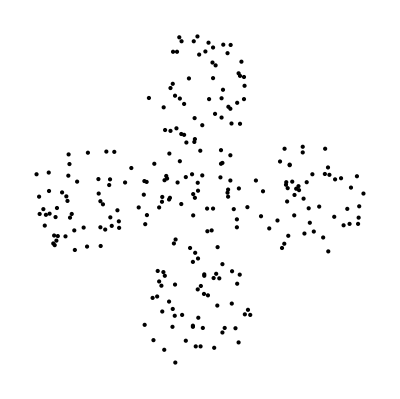

```mathematica
Graphics[Map[Point[#]&,sahaDrop[5,2]]]
```

```mathematica
(sahaEDist[5,2]=Outer[EuclideanDistance,saha[5,2],saha[5,2],1])//Dimensions
```

{250,250}

```mathematica
Export["saha_5_2.dmat",sahaEDist[5,2],"Table"]
```

saha_5_2.dmat

```mathematica
sahaDShort[5,2]=Import["saha_5_2.dshort","Table"];
```

```mathematica
sahaDShortZeroself[5,2]=ReplacePart[sahaDShort[5,2],{x_,x_}->0];
```

```mathematica
sahaCls[5,2]={Range[1,50],Range[51,100],Range[101,150],Range[151,200],Range[201,250]};
```

```mathematica
cDunn[sahaCls[5,2],sahaDShortZeroself[5,2]]
```

1.21695

階層クラスタリング

```mathematica
clAg=Agglomerate[sahaDrop[5,2]->Range[250],DistanceFunction->EuclideanDistance,Linkage->"Single"];
```

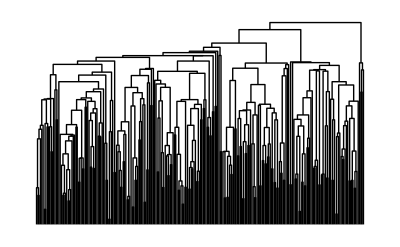

```mathematica
DendrogramPlot[clAg]
```

```mathematica
Map[ClusterFlatten[#]&,ClusterSplit[clAg,5]]
```

{{1,33,34,50,32,30,26,15,7,42,10,39,46,24,140,145,116,114,118,110,142,122,135,141,106,105,109,137,127,120,124,112,136,144,102,138,115,103,133,130,139,126,123,113,147,148,128,125,117,119,108,150,107,146,149,131,104,134,132,101,143,18,3,13,43,19,12,9,25,47,21,38,41,29,31,4,49,2,20,28,204,8,36,22,44,6,37,14,27,17,244,227,247,238,228,239,217,248,216,246,230,221,218,208,201,214,209,203,231,222,211,226,242,235,229,224,213,233,232,210,223,225,245,240,236,234,241,249,220,243,237,250,212,206,202,215,129,111,121},{219,207,205},{165,193,157,176,158,189,164,199,16,173,190,196,191,198,162,155,151,152,188,163,154,174,179,181,197,195,177,182,156,183,160,171,161,166,169,153,167,186,170,184,172,159,178,168,187,180,175,200,194,192,185},{48,5,23,96,60,56,90,81,73,71,63,65,52,68,62,54,78,84,97,77,11,35,45,40,64,79,51,100,58,74,76,67,61,88,92,75,91,66,85,57,83,98,80,89,53,55,59,72,86,95,70,93,94},{69,87,82,99}}

```mathematica
slRes[3]=FindClusters[sahaDrop[5,2]->Range[250],5,Method->"Agglomerate"]
```

{{1,2,3,4,6,7,8,9,10,12,13,14,15,17,18,19,20,21,22,24,25,26,27,28,29,30,31,32,33,34,36,37,38,39,41,42,43,44,46,47,49,50,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,201,202,203,204,206,208,209,210,211,212,213,214,215,216,217,218,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250},{5,11,23,35,40,45,48,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,70,71,72,73,74,75,76,77,78,79,80,81,83,84,85,86,88,89,90,91,92,93,94,95,96,97,98,100},{16,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200},{69,82,87,99},{205,207,219}}

```mathematica
cDunn[slRes[3],sahaDShortZeroself[5,2]]
```

0.331548

```mathematica
MinimumSpanningTree
```